# Time effect on temperature rise, dead mouse brain. Falling phase fits (141029)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141128 StdCon Mouse Variability

```mathematica
samplingRate=1000./128
```

7.8125

```mathematica
gagFiles=FileNames["*.mat"]
```

{140715-01-200um-5mW,500ms,0'2Hz,40T.mat,140722-01-200um-5mW,500ms,0'2Hz,40T.mat,140724-01-200um-5mW,500ms,0'2Hz,40T.mat,140908-01-200um-5mW,500ms,0'2Hz,40T.mat,140917-03-200um-5mW,500ms,0'2Hz,40T(No Blood vessel).mat}

## 5 mW 500 ms

## Functions

```mathematica
baselineNormalize[data_]:=Module[{},
(#-Mean[#[[1;;9]]])&/@data
];
```

```mathematica
meanBandPlot[data_, color_]:=Module[{means, sds},
means=Mean/@Transpose[data];
sds=StandardDeviation/@Transpose[data];
ListLinePlot[{means-sds, means+sds},
PlotStyle->None,
PlotRange->All,
Filling->{1->{{2},Opacity[1,color]}}
]
];
```

```mathematica
meanPlot[data_, color_, dataRange_:Automatic]:=
Module[{means,timePoints},
means=Mean/@Transpose[data];
If[dataRange===Automatic,
ListLinePlot[means,PlotStyle->{color,Thick}],
timePoints=Rescale[Range[Length[means]],{1,Length[means]},dataRange];
ListLinePlot[Transpose[{timePoints,means}],
PlotStyle->{color,Thick},PlotRange->All]
]


];
```

```mathematica
means[data_]:=Module[{means, sds},
Mean/@Transpose[data]
];
```

```mathematica
trialPointPlot[data_, color_]:=Module[{},
ListPlot[data,PlotStyle->Opacity[0.2,color]]
];
```

```mathematica
trialPointLogPlot[data_, color_]:=Module[{},
ListLogPlot[data,PlotStyle->Opacity[0.2,color]]
];
```

```mathematica
gagColors= {LightBlue,Blue,Darker[Blue],Purple,Pink,Red,Orange,Yellow,LightGreen,Green, Darker[Green]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
gagColors=Table[ColorData["GrayTones",1-n],{n,0.2,1,0.8/4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Load Data

```mathematica
gagFitDataStdConVar=Map[Import,gagFiles];
Dimensions/@gagFitDataStdConVar
```

{{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,40,620}}

```mathematica
gagFitDataStdConVar=Flatten[gagFitDataStdConVar,1];
Dimensions/@gagFitDataStdConVar
```

{{40,620},{40,620},{40,620},{40,620},{40,620}}

### Remove bad trials if necessary

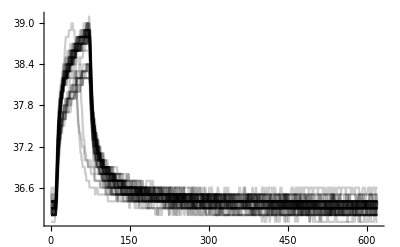
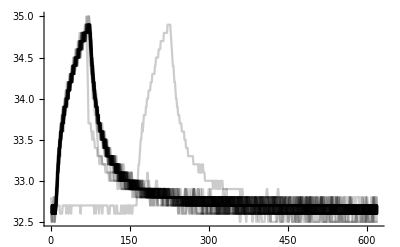
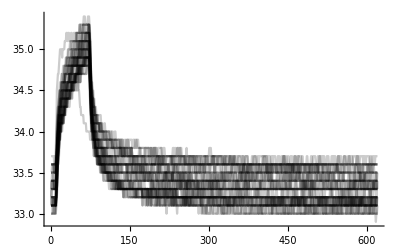
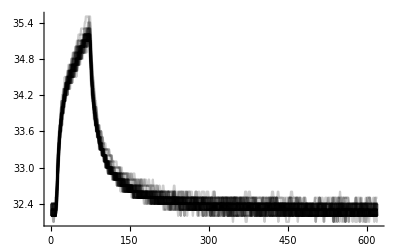
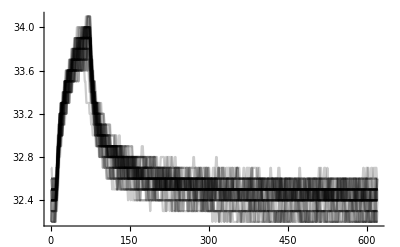

```mathematica
ListLinePlot[#,PlotStyle->Opacity[0.2,Black],PlotRange->All]&/@gagFitDataStdConVar
```

```mathematica
gagTemp=ListLinePlot[gagFitDataStdConVar[[3]],PlotStyle->Opacity[0.2,Black],PlotRange->All]
```

-Graphics-

```mathematica
Ordering[gagFitDataStdConVar[[3]][[;;, 1]],1]
```

{38}

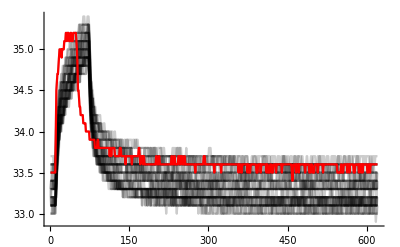

```mathematica
Show[gagTemp, ListLinePlot[gagFitDataStdConVar[[3]][[8]],PlotStyle->Red,PlotRange->All],PlotRange->All]
```

```mathematica
gagFitDataStdConVar[[1]]=Delete [gagFitDataStdConVar[[1]],{{33},{9},{2}}];
Dimensions[gagFitDataStdConVar[[1]]]
```

{37,620}

```mathematica
gagFitDataStdConVar[[2]]=Delete [gagFitDataStdConVar[[2]],{{16},{38}}];
Dimensions[gagFitDataStdConVar[[2]]]
```

{38,620}

```mathematica
gagFitDataStdConVar[[3]]=Delete [gagFitDataStdConVar[[3]],{{8}}];
Dimensions[gagFitDataStdConVar[[3]]]
```

{39,620}

```mathematica
Dimensions/@gagFitDataStdConVar
```

{{37,620},{38,620},{39,620},{40,620},{40,620}}

## Normalize Data so Baseline is at 0, Set Range Variables

```mathematica
Dimensions/@gagFitDataStdConVar
```

{{37,620},{38,620},{39,620},{40,620},{40,620}}

```mathematica
gagFitDataStdConVar=baselineNormalize/@ gagFitDataStdConVar;
```

```mathematica
Dimensions/@gagFitDataStdConVar
```

{{37,620},{38,620},{39,620},{40,620},{40,620}}

```mathematica
501/(1000/128.) (*figuring out stim duration*)
```

64.128

```mathematica
stimDuration=64;
stimStart=11;
stimEnd=stimStart+stimDuration-4;
fallStart=stimStart+stimDuration-1;
fallEnd=fallStart+200;
trialLength=Length[gagFitDataStdConVar[[1, 1]]]
```

620

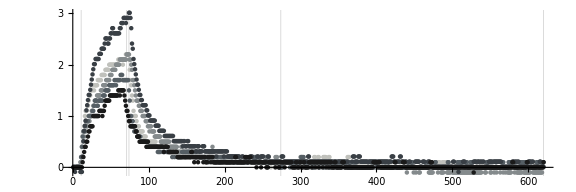

```mathematica
gagTempFitDataStdConVar=ListPlot[gagFitDataStdConVar[[All,1]],
GridLines->{{stimStart,stimEnd,fallStart,fallEnd,trialLength},None}, PlotRange->All,
AspectRatio->1/3, ImageSize->72*8,PlotStyle->gagColors]
```

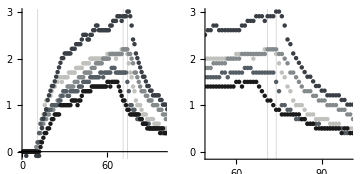

```mathematica
GraphicsRow[
{Show[gagTempFitDataStdConVar,PlotRange->{{0,100},All},AspectRatio->1],
Show[gagTempFitDataStdConVar,PlotRange->{stimStart+stimDuration+{-25,+25},All},AspectRatio->1]}, ImageSize->Medium]
```

## Cleaner Plots

```mathematica
Dimensions[Transpose[{gagFitDataStdConVar,gagColors}]]
```

{5,2}

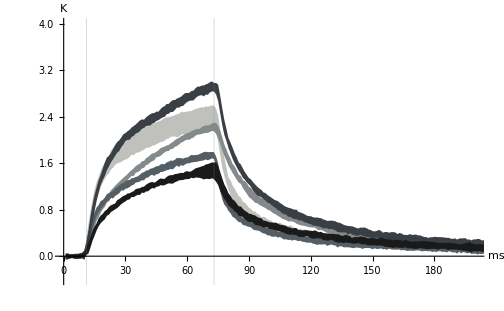

```mathematica
grSDStdConVar=Show[meanBandPlot[#[[1]],#[[2]]]& /@ Transpose[{gagFitDataStdConVar,gagColors}],
GridLines->{{stimStart,stimEnd+2},None}, PlotRange->{{0,200},{-0.4,4}},AspectRatio->1/GoldenRatio,ImageSize->72*7, AxesLabel->{"ms", "K"},Ticks->{Automatic,Automatic}, 
AxesStyle->Thickness[0.0025], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{0,0}]
```

```mathematica
legend={"1","2","3","4","5"};
```

```mathematica
gagLegend=SwatchLegend[gagColors,legend,LabelStyle->{FontSize->10,FontWeight->"Bold"},LegendMargins->5,LegendLayout->"Row",LegendLabel->"Mouse"]
```

```mathematica
(*gagLegend=BarLegend[{gagColors,{0,200}},LegendMarkers-> {{20,40}},LabelStyle->{FontSize->10,FontWeight->"Bold"},LegendMargins->5,LegendLayout->"Row",LegendLabel->"Lapsed Time [mins]"]*)
```

```mathematica
gagLegend=Graphics[
Table[
{gagColors[[n+1]],EdgeForm[Directive[Thin,Black]],Rectangle[{-10+n*20, 0},{10+n*20, 5}], Black, Text[legend[[n+1]],{n*20, 0},{0,1.5},BaseStyle->{FontSize->9,Bold}]}, 
{n,0,4}], PlotLabel->Style["Mouse",FontWeight->Bold,FontSize->9,FontColor->Black], AspectRatio->1/10,ImageSize->72*1.5
]
```

-Graphics-

```mathematica
(*gagLegend=BarLegend[{gagColors,{-10,210}},10,LabelStyle->{FontSize->10,FontWeight->"Bold"},LegendMargins->5,LegendLayout->"Row",LegendLabel->"Lapsed Time [mins]"]*)
```

```mathematica
(*gagLegend2= SwatchLegend[{Opacity[0.15,Blue]}, {"Laser Stimulation"},LabelStyle->{FontSize->10,FontWeight->"Bold"},LegendMargins->{{53,54},{5,5}},LegendLayout->"Row",LegendFunction->(Framed[#]&)]*)
```

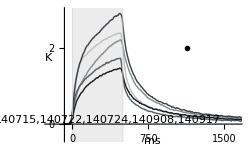

```mathematica
grSDStdConVar=Show[
Show[meanPlot[#[[1]],#[[2]],{-11,620-11}*samplingRate]& /@ Transpose[{gagFitDataStdConVar,gagColors}],ImageSize->72*3.5,
GridLines->{{0,500},None},GridLinesStyle->Thickness[0.0025],PlotRange->{{-30,210}*samplingRate,{-0.4,3}},AspectRatio->1/GoldenRatio, AxesLabel->{None, None},Ticks->{Table[n,{n,0,1500,250}],Table[n,{n,0,3,1}]},TicksStyle->Directive[Black,9],
AxesStyle->Thickness[0.004], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{-10*samplingRate,0},LabelStyle->{FontSize->9,FontWeight->"Bold"},
(*PlotLabel->  "Average temperature increase through time",*)
Prolog->{Opacity[0.15,Gray], Rectangle[{0,-0.7},{500,4.3}]},
Epilog->{Text["ms",{101*samplingRate,-0.45},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Text["K",{-30*samplingRate,1.75},BaseStyle->{FontSize->9,FontWeight->"Bold"}],
Inset[gagLegend,{145*samplingRate,2}],Text["140715,140722,140724,140908,140917",{45*samplingRate,0.1},BaseStyle->{FontSize->2}]}]
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141128 StdCon Mouse Variability

```mathematica
Export["141128.AverageStdConVar.png",grSDStdConVar,ImageResolution->600]
```

141128.AverageStdConVar.png

```mathematica
Export["141128.AverageStdConVar.pdf",grSDStdConVar,ImageResolution->600]
```

141128.AverageStdConVar.pdf

```mathematica
gagMeanDataStdConVar= Mean/@gagFitDataStdConVar;
```

```mathematica
Dimensions[gagMeanDataStdConVar]
```

{5,620}

```mathematica
gagMaxDataStdConVar=Max/@gagMeanDataStdConVar
```

{2.3973,2.22076,1.73732,2.91889,1.47611}

```mathematica
gagMaxDataStdConVar=Map[ToString[NumberForm[#,{3,2}],OutputForm]&,gagMaxDataStdConVar,{1}]
```

{2.40,2.22,1.74,2.92,1.48}

```mathematica
gagMaxDataStdConVar=ToExpression[gagMaxDataStdConVar]
```

{2.4,2.22,1.74,2.92,1.48}

```mathematica
gagTotalAvgTempStdConVar=Mean[gagMaxDataStdConVar]
```

2.152

```mathematica
Options[BarChart]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BarOrigin→Bottom,BarSpacing→Automatic,BaselinePosition→Automatic,BaseStyle→{},ChartBaseStyle→Automatic,ChartElementFunction→Automatic,ChartElements→Automatic,ChartLabels→None,ChartLayout→Automatic,ChartLegends→None,ChartStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,Joined→False,LabelingFunction→Automatic,LabelStyle→{},LegendAppearance→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

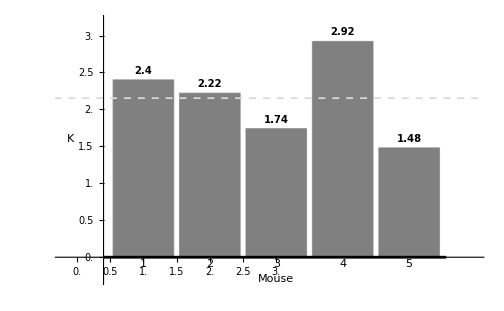

```mathematica
gagMaxTempGraph=BarChart[gagMaxDataStdConVar,
PlotRange->{{-0.2,6},{-0.3,3.2}},
GridLines->{None,{{gagTotalAvgTempStdConVar,Dashed}}},GridLinesStyle->Thickness[0.0025],
ChartLabels->{{"1","2","3","4","5"}},
AspectRatio->1/GoldenRatio,ImageSize->72*7,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->12],Directive[Black,Thickness[0.004],FontSize->12]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->12,FontWeight->Bold},AxesOrigin->{0.4,0},
Ticks->{Table[n,{n,0,3,0.5}]},ChartStyle->Gray,TicksStyle->Bold,
LabelingFunction->Above,LabelStyle->{FontWeight->Bold,FontSize->10},
Epilog->{Text["Mouse",{3,-0.3},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Text["K",{-0.1,1.6},BaseStyle->{FontSize->12,FontWeight->"Bold"}]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141128 StdCon Mouse Variability

```mathematica
Export["141128.StdConVarMaxTemp.png",gagMaxTempGraph]
```

141128.StdConVarMaxTemp.png

```mathematica
Export["141128.StdConVarMaxTemp.pdf",gagMaxTempGraph]
```

141128.StdConVarMaxTemp.pdf

## Change data to {{time,value}, ....} format and Fit Functions

```mathematica
gagMakeTrialXY[data_, startPoint_Integer, endPoint_Integer]:=Module[{gagTimecourseR},
gagTimecourseR =Range[0, endPoint-startPoint ] *samplingRate;
Flatten[ 
Transpose[{gagTimecourseR,#[[startPoint;;endPoint]]}]&  /@ data,   1
]
];
```

```mathematica
gagModelModelRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc, tempShift},
Simplify[Evaluate[
NonlinearModelFit[gagMakeTrialXY[data,startPoint, endPoint],  
{0.4*a*Log[0.01*c* x+0.1*b]},
{a,b,c},x]]] 
];
```

```mathematica
gagModelShiftFactorRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc,tempShift},
tempFunc=gagModelFuncRLog[data, startPoint, endPoint];
tempShift= x /. Flatten[Solve[ Evaluate[tempFunc[x]]==0, x]];
tempShift
];
```

```mathematica
gagModelFuncRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc},
tempFunc=gagModelModelRLog[data, startPoint, endPoint]["BestFit"];
Evaluate[tempFunc /. x->#]&
];
```

```mathematica
gagModelModelFExp[data_, startPoint_Integer, endPoint_Integer]:=
Module[{},
Simplify[Evaluate[
NonlinearModelFit[gagMakeTrialXY[data,startPoint, endPoint],  
{a*ⅇ^(b*(x+7)) +aa*ⅇ^(b*bb*(x+90)),{0 < a<5,-0.5<b<-0.0001 ,0<aa<5,0<bb<1}},
{a,c,b,aa,bb,cc},x]]]
];
```

```mathematica
gagModelFuncFExp[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc},
tempFunc=gagModelModelFExp[data, startPoint, endPoint]["BestFit"] ;
Evaluate[tempFunc /. x->#]&
];
```

```mathematica
Manipulate[
Show[grSDStdConVar,Plot[a*ⅇ^(b*(x)) +aa*ⅇ^(bb*(x)),{x,fallStart,trialLength},PlotRange->All],
PlotRange->All],
{{a,230.},0,1500},{{b,-0.0612},-0.2,0.2},{{aa,0.31},0,5},{{bb,0.0075},-1,0.3}
];
```

## Fit Function BootStrap

```mathematica
gagBootStrapData=Table[RandomSample[#,10],{500}]& /@gagFitDataStdConVar;
Dimensions[gagBootStrapData]
```

{5,500,10,620}

```mathematica
gagBootStrapModel= ParallelMap[gagModelModelRLog[#,stimStart, stimEnd]&, gagBootStrapData[[#]]]& /@Range[5];
Dimensions[gagBootStrapModel]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{5,500}

```mathematica
gagBootStrapModelParams=#["BestFitParameters"]&/@gagBootStrapModel[[#]]&/@Table[x,{x,1,5,1}];
Dimensions[gagBootStrapModelParams]
```

{5,500,3}

```mathematica
gagBootStrapModelParams=Transpose[gagBootStrapModelParams,{1,3,2}];
Dimensions[gagBootStrapModelParams]
```

{5,3,500}

```mathematica
gagBootStrapModelParams={a/.#& /@gagBootStrapModelParams[[;;,1,#]]*0.4&/@Table[x,{x,1,500,1}],b/.#& /@gagBootStrapModelParams[[;;,2,#]]*0.1&/@Table[x,{x,1,500,1}],c/.#& /@gagBootStrapModelParams[[;;,3,#]]*0.01&/@Table[x,{x,1,500,1}]};
Dimensions[gagBootStrapModelParams]
```

{3,500,5}

```mathematica
gagBootStrapModelParams=Transpose[gagBootStrapModelParams,{1,3,2}];
Dimensions[gagBootStrapModelParams]
```

{3,5,500}

```mathematica
gagBootStrapModelParams=Transpose[gagBootStrapModelParams,{2,1,3}];
Dimensions[gagBootStrapModelParams]
```

{5,3,500}

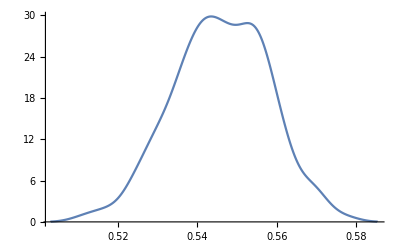
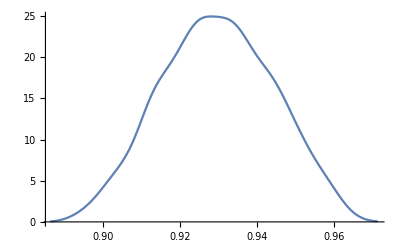
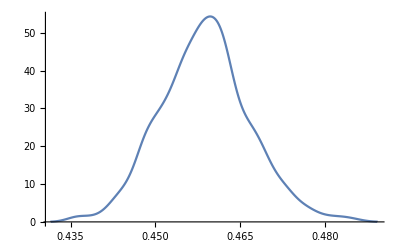
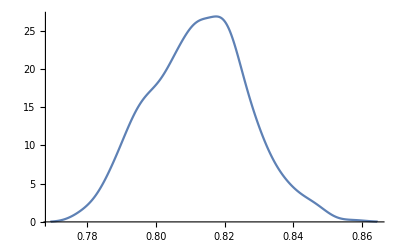
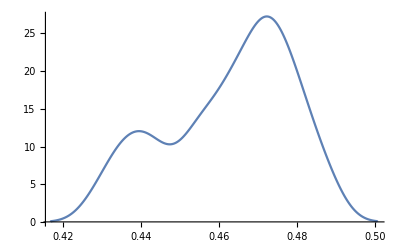
5
6[{{-Graphics-,0.295589},{-Graphics-,0.252554},{-Graphics-,0.160705},{-Graphics-,0.277927},{-Graphics-,0}}]

```mathematica
{SmoothHistogram[gagBootStrapModelParams[[#,1]]],DistributionFitTest[gagBootStrapModelParams[[#,1]]]}&/@Table[x,{x,1,5,1}]//TableForm[{5,6}]
```

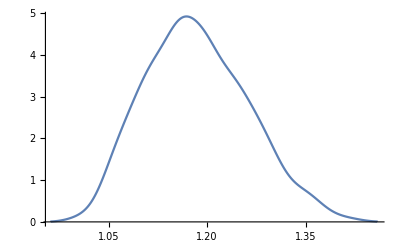
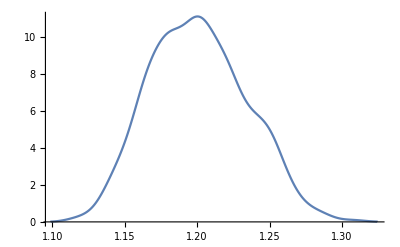
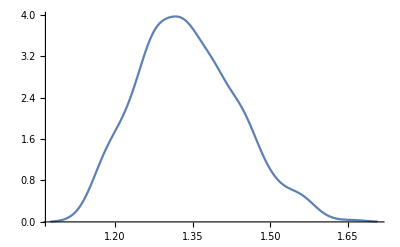
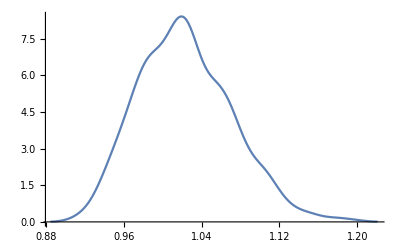
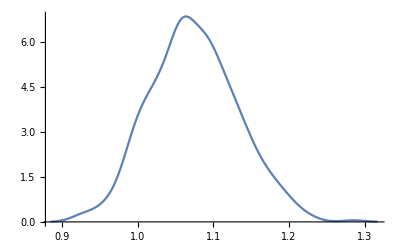
5
6[{{-Graphics-,0.295589},{-Graphics-,0.252554},{-Graphics-,0.160705},{-Graphics-,0.277927},{-Graphics-,0}}]

```mathematica
{SmoothHistogram[gagBootStrapModelParams[[#,2]]],DistributionFitTest[gagBootStrapModelParams[[#,1]]]}&/@Table[x,{x,1,5,1}]//TableForm[{5,6}]
```

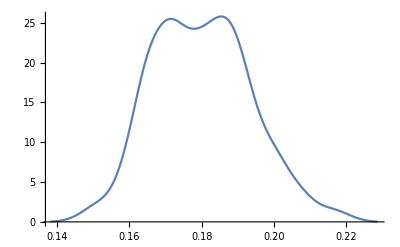
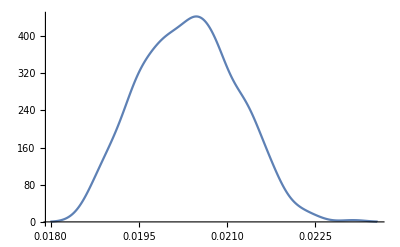
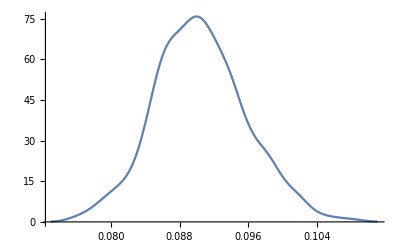
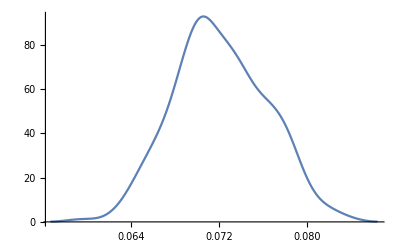
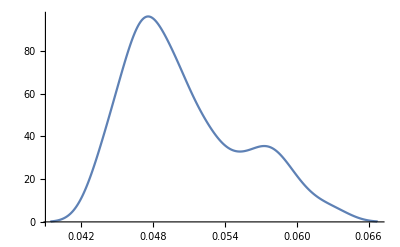
5
6[{{-Graphics-,0.295589},{-Graphics-,0.252554},{-Graphics-,0.160705},{-Graphics-,0.277927},{-Graphics-,0}}]

```mathematica
{SmoothHistogram[gagBootStrapModelParams[[#,3]]],DistributionFitTest[gagBootStrapModelParams[[#,1]]]}&/@Table[x,{x,1,5,1}]//TableForm[{5,6}]
```

```mathematica
gagBootStrapModelParamsMedian=Transpose[Median[#]&/@gagBootStrapModelParams[[#]]&/@Range[5]];
Dimensions[gagBootStrapModelParamsMedian]
```

{3,5}

```mathematica
gagBootStrapModelParams99= Transpose[Quantile[#,{0.01,0.99},{{1/2,0},{0,1}}]&/@gagBootStrapModelParams[[#]]&/@Range[5],{1,2,3}];
Dimensions[gagBootStrapModelParams99]
```

{5,3,2}

```mathematica
gagBootStrapModelParamsMedian0=gagBootStrapModelParamsMedian
```

{{0.546182,0.929635,0.458661,0.812605,0.466238},{1.17785,1.19943,1.33275,1.01915,1.07144},{0.17944,0.0203445,0.090123,0.0719258,0.0493791}}

```mathematica
gagBootStrapModelParamsMedian0={Table[n,{n,1,5,2}],gagBootStrapModelParamsMedian0[[;;,#]]}&/@Range[5]
Dimensions[gagBootStrapModelParamsMedian0]
```

{{{1,3,5},{0.546182,1.17785,0.17944}},{{1,3,5},{0.929635,1.19943,0.0203445}},{{1,3,5},{0.458661,1.33275,0.090123}},{{1,3,5},{0.812605,1.01915,0.0719258}},{{1,3,5},{0.466238,1.07144,0.0493791}}}

{5,2,3}

```mathematica
Transpose[gagBootStrapModelParamsMedian0,{1,3,2}]
```

{{{1,0.546182},{3,1.17785},{5,0.17944}},{{1,0.929635},{3,1.19943},{5,0.0203445}},{{1,0.458661},{3,1.33275},{5,0.090123}},{{1,0.812605},{3,1.01915},{5,0.0719258}},{{1,0.466238},{3,1.07144},{5,0.0493791}}}

```mathematica
gagBootStrapModelParamsMedian0=Transpose[gagBootStrapModelParamsMedian0,{1,3,2}]
```

{{{1,0.546182},{3,1.17785},{5,0.17944}},{{1,0.929635},{3,1.19943},{5,0.0203445}},{{1,0.458661},{3,1.33275},{5,0.090123}},{{1,0.812605},{3,1.01915},{5,0.0719258}},{{1,0.466238},{3,1.07144},{5,0.0493791}}}

```mathematica
gagBootStrapModelParamsMedian0
```

{{{1,0.546182},{3,1.17785},{5,0.17944}},{{1,0.929635},{3,1.19943},{5,0.0203445}},{{1,0.458661},{3,1.33275},{5,0.090123}},{{1,0.812605},{3,1.01915},{5,0.0719258}},{{1,0.466238},{3,1.07144},{5,0.0493791}}}

```mathematica
gagBootStrapModelParamsMedian0[[;;,1,1]]=gagBootStrapModelParamsMedian0[[;;,1,1]]+Table[n,{n,-0.3,0.9,0.3}]
```

{0.7,1.,1.3,1.6,1.9}

```mathematica
gagBootStrapModelParamsMedian0[[;;,2,1]]=gagBootStrapModelParamsMedian0[[;;,2,1]]+Table[n,{n,-0.3,0.9,0.3}]
```

{2.7,3.,3.3,3.6,3.9}

```mathematica
gagBootStrapModelParamsMedian0[[;;,3,1]]=gagBootStrapModelParamsMedian0[[;;,3,1]]+Table[n,{n,-0.3,0.9,0.3}]
```

{4.7,5.,5.3,5.6,5.9}

```mathematica
gagBootStrapModelParamsMedian0
```

{{{0.7,0.546182},{2.7,1.17785},{4.7,0.17944}},{{1.,0.929635},{3.,1.19943},{5.,0.0203445}},{{1.3,0.458661},{3.3,1.33275},{5.3,0.090123}},{{1.6,0.812605},{3.6,1.01915},{5.6,0.0719258}},{{1.9,0.466238},{3.9,1.07144},{5.9,0.0493791}}}

```mathematica
gagBootStrapModelParams99-gagBootStrapModelParamsMedian0[[;;,;;,2]]
```

{{{-0.0299052,0.0260585},{-0.138977,0.194909},{-0.0290377,0.0357659}},{{-0.0312132,0.0298594},{-0.063698,0.0808332},{-0.00161875,0.00186632}},{{-0.0181156,0.0206988},{-0.171421,0.237115},{-0.0116828,0.0133516}},{{-0.0307258,0.0337753},{-0.087128,0.131557},{-0.00891268,0.00997126}},{{-0.0382175,0.0233211},{-0.128975,0.139602},{-0.00642062,0.0133439}}}

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
gagAvalueBootStrapGraph=ErrorListPlot[
Transpose[{gagBootStrapModelParamsMedian0,
Map[ErrorBar,
(gagBootStrapModelParams99-gagBootStrapModelParamsMedian0[[;;,;;,2]]),
{2}
]
},{3,2,1}],

Joined->True,
PlotRange->{{-0.3,7},{-0.3,1.7}},AspectRatio->1/GoldenRatio,AxesStyle->Thickness[0.004], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{0.5,0},LabelStyle->{FontSize->12,FontWeight->"Bold"},
PlotMarkers->{Automatic,Medium},
PlotLegends-> Placed[LineLegend[{"a","b","c"},LegendMarkers->{Automatic},LegendLabel->Style["Parameters",FontWeight->Bold]],{{1,0.5},{1.5,0.5}}],
PlotStyle->{Gray,Directive[Gray,Dashed],Directive[Gray,DotDashed]},Ticks->{{{1,"a"},{3,"b"},{5,"c"}},{0,0.25,0.5,0.75,1,1.25,1.5}},Epilog->{Text["Mouse",{3.2,-0.2},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Rotate[Text["Model Parameters",{-0.15,0.90},BaseStyle->{FontSize->12,FontWeight->"Bold"}],90 Degree]}
]
```

-Graphics-

```mathematica
gagBootStrapModelParamsMedian0
```

{{{0.7,0.546182},{2.7,1.17785},{4.7,0.17944}},{{1.,0.929635},{3.,1.19943},{5.,0.0203445}},{{1.3,0.458661},{3.3,1.33275},{5.3,0.090123}},{{1.6,0.812605},{3.6,1.01915},{5.6,0.0719258}},{{1.9,0.466238},{3.9,1.07144},{5.9,0.0493791}}}

```mathematica
gagBootStrapModelParamsMedian1=Transpose[Median[#]&/@gagBootStrapModelParams[[#]]&/@Range[5]]
```

{{0.546182,0.929635,0.458661,0.812605,0.466238},{1.17785,1.19943,1.33275,1.01915,1.07144},{0.17944,0.0203445,0.090123,0.0719258,0.0493791}}

```mathematica
gagBootStrapModelParamsMedian1=ToString[NumberForm[#,{3,2}]]&/@gagBootStrapModelParamsMedian1
```

{{0.55, 0.93, 0.46, 0.81, 0.47},{1.18, 1.20, 1.33, 1.02, 1.07},{0.18, 0.02, 0.09, 0.07, 0.05}}

```mathematica
gagBootStrapModelParamsMedian1=ToExpression[gagBootStrapModelParamsMedian1]
Dimensions[gagBootStrapModelParamsMedian1]
```

{{0.55,0.93,0.46,0.81,0.47},{1.18,1.2,1.33,1.02,1.07},{0.18,0.02,0.09,0.07,0.05}}

{3,5}

```mathematica
gagBootStrapModelParams991=ToString[NumberForm[#,{3,2}]]&/@gagBootStrapModelParams99
```

{{{0.52, 0.57}, {1.04, 1.37}, {0.15, 0.22}},{{0.90, 0.96}, {1.14, 1.28}, {0.02, 0.02}},{{0.44, 0.48}, {1.16, 1.57}, {0.08, 0.10}},{{0.78, 0.85}, {0.93, 1.15}, {0.06, 0.08}},{{0.43, 0.49}, {0.94, 1.21}, {0.04, 0.06}}}

```mathematica
gagBootStrapModelParams991=ToExpression[gagBootStrapModelParams991]
Dimensions[gagBootStrapModelParams991]
```

{{{0.52,0.57},{1.04,1.37},{0.15,0.22}},{{0.9,0.96},{1.14,1.28},{0.02,0.02}},{{0.44,0.48},{1.16,1.57},{0.08,0.1}},{{0.78,0.85},{0.93,1.15},{0.06,0.08}},{{0.43,0.49},{0.94,1.21},{0.04,0.06}}}

{5,3,2}

```mathematica
gagBootStrapModelParams991=Transpose[gagBootStrapModelParams991,{2,1,3}]
```

{{{0.52,0.57},{0.9,0.96},{0.44,0.48},{0.78,0.85},{0.43,0.49}},{{1.04,1.37},{1.14,1.28},{1.16,1.57},{0.93,1.15},{0.94,1.21}},{{0.15,0.22},{0.02,0.02},{0.08,0.1},{0.06,0.08},{0.04,0.06}}}

```mathematica
gagBootStrapModelParams991=gagBootStrapModelParams991-gagBootStrapModelParamsMedian1
```

{{{-0.03,0.02},{-0.03,0.03},{-0.02,0.02},{-0.03,0.04},{-0.04,0.02}},{{-0.14,0.19},{-0.06,0.08},{-0.17,0.24},{-0.09,0.13},{-0.13,0.14}},{{-0.03,0.04},{0.,0.},{-0.01,0.01},{-0.01,0.01},{-0.01,0.01}}}

```mathematica
gagCValueBootStrapData=Table[gagBootStrapModelParamsMedian1[[i,j]]->gagBootStrapModelParams991[[i,j]],{i,1,Length[gagBootStrapModelParamsMedian1]},{j,1,Length[gagBootStrapModelParamsMedian1[[1]]]}]
```

{{0.55→{-0.03,0.02},0.93→{-0.03,0.03},0.46→{-0.02,0.02},0.81→{-0.03,0.04},0.47→{-0.04,0.02}},{1.18→{-0.14,0.19},1.2→{-0.06,0.08},1.33→{-0.17,0.24},1.02→{-0.09,0.13},1.07→{-0.13,0.14}},{0.18→{-0.03,0.04},0.02→{0.,0.},0.09→{-0.01,0.01},0.07→{-0.01,0.01},0.05→{-0.01,0.01}}}

```mathematica
errorBar[type_:"Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{errorN,errorP},{errorN=Flatten[meta],errorP=Flatten[meta]};
{errorN,errorP}=If[{errorN,errorP}==={},0,Last[{errorN,errorP}]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Thickness[0.0035],Line[{{{(x0+x1)/2,y1+errorN},{(x0+x1)/2,y1+errorP}},{{1/4 (3 x0+x1),y1+errorP},{1/4 (x0+3 x1),y1+errorP}},{{1/4 (3 x0+x1),y1+errorN},{1/4 (x0+3 x1),y1+errorN}}}]}}]
```

```mathematica
gagLegend2=SwatchLegend[{GrayLevel[0.25],GrayLevel[0.5],GrayLevel[0.8]},{"a","b","c"},LabelStyle->{FontSize->9,FontWeight->"Bold"},LegendMargins->5,LegendLayout->"Column",LegendLabel->"Parameters"]
```

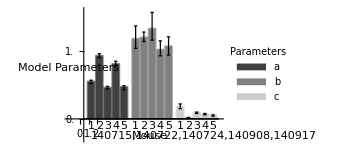

```mathematica
gagCValueBootStrapGraph=BarChart[{gagCValueBootStrapData[[1]],gagCValueBootStrapData[[2]],gagCValueBootStrapData[[3]]},ChartElementFunction->errorBar["Rectangle"],ImageSize->72*3.5,
PlotRange->{{-1.5,17},{-0.3,1.6}},
ChartLabels->{{"1","2","3","4","5"}},LabelStyle->{FontSize->9,FontWeight->"Bold"},BarSpacing->{0.2,0.7},ChartBaseStyle->EdgeForm[Thickness[0.0058]],
AspectRatio->1/GoldenRatio,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->12],Directive[Black,Thickness[0.004],FontSize->12]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->9,FontWeight->Bold},AxesOrigin->{0.4,0},
Ticks->{Table[n,{n,0,2,0.5}]},TicksStyle->Directive[Black,9],ChartStyle->{{GrayLevel[0.25],GrayLevel[0.5],GrayLevel[0.8]},None},TicksStyle->Bold,LabelStyle->{FontWeight->Bold,FontSize->9},
Epilog->{Text["Mouse",{8.5,-0.25},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Rotate[Text["Model Parameters",{-1.4,0.75},BaseStyle->{FontSize->9,FontWeight->"Bold"}],90 Degree],Inset[gagLegend2,{15,1}],Text["140715,140722,140724,140908,140917",{15,-0.25},BaseStyle->{FontSize->2}]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141128 StdCon Mouse Variability

```mathematica
Export["141128.ModelParametersStdConVarBootStrap.png",gagCValueBootStrapGraph,ImageResolution->600]
```

141128.ModelParametersStdConVarBootStrap.png

```mathematica
Export["141128.ModelParametersStdConVarBootStrap.pdf",gagCValueBootStrapGraph,ImageResolution->600]
```

141128.ModelParametersStdConVarBootStrap.pdf

```mathematica
gagBootStrapModelParamsMedian
Dimensions[gagBootStrapModelParamsMedian]
```

{{0.546182,0.929635,0.458661,0.812605,0.466238},{1.17785,1.19943,1.33275,1.01915,1.07144},{0.17944,0.0203445,0.090123,0.0719258,0.0493791}}

{3,5}

```mathematica
gagBootStrapModelParams99
Dimensions[gagBootStrapModelParams99]
```

{{{0.516277,0.57224},{1.03887,1.37276},{0.150402,0.215206}},{{0.898422,0.959495},{1.13574,1.28027},{0.0187258,0.0222109}},{{0.440546,0.47936},{1.16133,1.56987},{0.0784402,0.103475}},{{0.781879,0.846381},{0.932026,1.15071},{0.0630131,0.081897}},{{0.428021,0.489559},{0.942469,1.21105},{0.0429585,0.0627231}}}

{5,3,2}

```mathematica
Transpose[{gagBootStrapModelParamsMedian,Transpose[gagBootStrapModelParams99,{2,1,3}]},{3,1,2}]
```

{{{0.546182,{0.516277,0.57224}},{0.929635,{0.898422,0.959495}},{0.458661,{0.440546,0.47936}},{0.812605,{0.781879,0.846381}},{0.466238,{0.428021,0.489559}}},{{1.17785,{1.03887,1.37276}},{1.19943,{1.13574,1.28027}},{1.33275,{1.16133,1.56987}},{1.01915,{0.932026,1.15071}},{1.07144,{0.942469,1.21105}}},{{0.17944,{0.150402,0.215206}},{0.0203445,{0.0187258,0.0222109}},{0.090123,{0.0784402,0.103475}},{0.0719258,{0.0630131,0.081897}},{0.0493791,{0.0429585,0.0627231}}}}

```mathematica
gagBootStrapModelParamsMedian=Transpose[{gagBootStrapModelParamsMedian,Transpose[gagBootStrapModelParams99,{2,1,3}]},{3,1,2}]
```

{{{0.546182,{0.516277,0.57224}},{0.929635,{0.898422,0.959495}},{0.458661,{0.440546,0.47936}},{0.812605,{0.781879,0.846381}},{0.466238,{0.428021,0.489559}}},{{1.17785,{1.03887,1.37276}},{1.19943,{1.13574,1.28027}},{1.33275,{1.16133,1.56987}},{1.01915,{0.932026,1.15071}},{1.07144,{0.942469,1.21105}}},{{0.17944,{0.150402,0.215206}},{0.0203445,{0.0187258,0.0222109}},{0.090123,{0.0784402,0.103475}},{0.0719258,{0.0630131,0.081897}},{0.0493791,{0.0429585,0.0627231}}}}

```mathematica
Dimensions[gagBootStrapModelParamsMedian]
```

{3,5,2}

```mathematica
gagBootStrapModelParamsMedian=Map[(ToString[NumberForm[#[[1]],{3,2}]] <> " ("<>ToString[NumberForm[#[[2,1]],{3,2}]]<>"-"<>ToString[NumberForm[#[[2,2]],{3,2}]]<>")" )&, gagBootStrapModelParamsMedian,{2}]
```

{{0.55 (0.52-0.57),0.93 (0.90-0.96),0.46 (0.44-0.48),0.81 (0.78-0.85),0.47 (0.43-0.49)},{1.18 (1.04-1.37),1.20 (1.14-1.28),1.33 (1.16-1.57),1.02 (0.93-1.15),1.07 (0.94-1.21)},{0.18 (0.15-0.22),0.02 (0.02-0.02),0.09 (0.08-0.10),0.07 (0.06-0.08),0.05 (0.04-0.06)}}

```mathematica
gagBootStrapModelParamsMedian=Prepend[gagBootStrapModelParamsMedian,{"Mouse",1,2,3,4,5}];
Dimensions[gagBootStrapModelParamsMedian]
```

{4}

```mathematica
gagBootStrapModelParamsMedian[[2]]
```

{0.55 (0.52-0.57),0.93 (0.90-0.96),0.46 (0.44-0.48),0.81 (0.78-0.85),0.47 (0.43-0.49)}

```mathematica
gagBootStrapModelParamsMedian[[2]]= Prepend[gagBootStrapModelParamsMedian[[2]],"a (1%CI-99%CI)"];
```

```mathematica
gagBootStrapModelParamsMedian[[3]]= Prepend[gagBootStrapModelParamsMedian[[3]],"b (1%CI-99%CI)"];
```

```mathematica
gagBootStrapModelParamsMedian[[4]]= Prepend[gagBootStrapModelParamsMedian[[4]],"c (1%CI-99%CI)"];
```

```mathematica
Options[Grid]
```

{Alignment→{Center,Baseline},AllowedDimensions→Automatic,AllowScriptLevelChange→True,AutoDelete→False,Background→None,BaselinePosition→Automatic,BaseStyle→{},DefaultBaseStyle→Grid,DefaultElement→□,DeleteWithContents→True,Dividers→{},Editable→Automatic,Frame→None,FrameStyle→Automatic,ItemSize→Automatic,ItemStyle→None,Selectable→Automatic,Spacings→Automatic}

```mathematica
gagBootStrapModelParamsMedian//InputForm
```

{{"Mouse", 1, 2, 3, 4, 5}, {"a (1%CI-99%CI)", "0.55 (0.52-0.57)", "0.93 (0.90-0.96)", "0.46 (0.44-0.48)", "0.81 (0.78-0.85)", "0.47 (0.43-0.49)"}, 
 {"b (1%CI-99%CI)", "1.18 (1.04-1.37)", "1.20 (1.14-1.28)", "1.33 (1.16-1.57)", "1.02 (0.93-1.15)", "1.07 (0.94-1.21)"}, {"c (1%CI-99%CI)", "0.18 (0.15-0.22)", "0.02 (0.02-0.02)", "0.09 (0.08-0.10)", "0.07 (0.06-0.08)", 
  "0.05 (0.04-0.06)"}}

```mathematica
gagParamsTableBootStrap=Grid[gagBootStrapModelParamsMedian,Frame->All,ItemSize->{{1->9,2;;12->8},1.5},BaseStyle->{FontSize->9,FontFamily->"Helvetica"},ItemStyle->{{Bold},{Directive[Bold,FontFamily->"Helvetica"],FontFamily->"Helvetica",FontFamily->"Helvetica",FontFamily->"Helvetica"}},Dividers->{{2->Thick},{2->Thick}},Background->{None,None}(*,BaseStyle{FontFamily->"Helvetica"}*)]
```

Mouse | 1 | 2 | 3 | 4 | 5
a (1%CI-99%CI) | 0.55 (0.52-0.57) | 0.93 (0.90-0.96) | 0.46 (0.44-0.48) | 0.81 (0.78-0.85) | 0.47 (0.43-0.49)
b (1%CI-99%CI) | 1.18 (1.04-1.37) | 1.20 (1.14-1.28) | 1.33 (1.16-1.57) | 1.02 (0.93-1.15) | 1.07 (0.94-1.21)
c (1%CI-99%CI) | 0.18 (0.15-0.22) | 0.02 (0.02-0.02) | 0.09 (0.08-0.10) | 0.07 (0.06-0.08) | 0.05 (0.04-0.06)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141128 StdCon Mouse Variability

```mathematica
Export["141128.ParamsTableStdConVarBootStrap.png",gagParamsTableBootStrap,ImageResolution->600]
```

141128.ParamsTableStdConVarBootStrap.png

```mathematica
Export["141128.ParamsTableStdConVarBootStrap.pdf",gagParamsTableBootStrap,ImageResolution->600]
```

141128.ParamsTableStdConVarBootStrap.pdf

## Fit Function

```mathematica
{funcR1,funcR2, funcR3, funcR4,funcR5}=gagModelFuncRLog[#,stimStart, stimEnd]& /@gagFitDataStdConVar
```

{0.545221 Log[1.18724+0.180204 #1]&,0.928331 Log[1.20176+0.0203881 #1]&,0.458006 Log[1.33477+0.0904405 #1]&,0.812446 Log[1.02237+0.0719882 #1]&,0.463089 Log[1.06781+0.0500459 #1]&}

```mathematica
{modelR1,modelR2, modelR3, modelR4,modelR5}=gagModelModelRLog[#,stimStart, stimEnd]& /@gagFitDataStdConVar;
```

```mathematica
gagModelParams={modelR1["BestFitParameters"],modelR2["BestFitParameters"],modelR3["BestFitParameters"],modelR4["BestFitParameters"],modelR5["BestFitParameters"]};
```

```mathematica
gagModelParams=Transpose[gagModelParams]
```

{{a→1.36305,a→2.32083,a→1.14502,a→2.03112,a→1.15772},{b→11.8724,b→12.0176,b→13.3477,b→10.2237,b→10.6781},{c→18.0204,c→2.03881,c→9.04405,c→7.19882,c→5.00459}}

```mathematica
gagModelParams={a/.#& /@gagModelParams[[1]]*0.4,b/.#& /@gagModelParams[[2]]*0.1,c/.#& /@gagModelParams[[3]]*0.01}
```

{{0.545221,0.928331,0.458006,0.812446,0.463089},{1.18724,1.20176,1.33477,1.02237,1.06781},{0.180204,0.0203881,0.0904405,0.0719882,0.0500459}}

```mathematica
gagModelParams0=gagModelParams
```

{{0.545221,0.928331,0.458006,0.812446,0.463089},{1.18724,1.20176,1.33477,1.02237,1.06781},{0.180204,0.0203881,0.0904405,0.0719882,0.0500459}}

```mathematica
gagModelParams=Map[ToString[NumberForm[#,{4,3}]]&,gagModelParams,{2}]
```

{{0.545,0.928,0.458,0.812,0.463},{1.187,1.202,1.335,1.022,1.068},{0.180,0.020,0.090,0.072,0.050}}

```mathematica
gagModelParams1=ToExpression[gagModelParams]
```

{{0.545,0.928,0.458,0.812,0.463},{1.187,1.202,1.335,1.022,1.068},{0.18,0.02,0.09,0.072,0.05}}

```mathematica
Options[ListLinePlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→True,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

```mathematica
gagAvalueGraph=ListLinePlot[
gagModelParams0, 
PlotRange->{{-0.3,7},{-0.3,1.7}},AspectRatio->1/GoldenRatio,ImageSize->72*7,AxesStyle->Thickness[0.004], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{0.5,0},LabelStyle->{FontSize->12,FontWeight->"Bold"},
PlotMarkers->{Automatic,Medium},
PlotLegends-> Placed[LineLegend[{"a","b","c"},LegendMarkers->{Automatic},LegendLabel->Style["Parameters",FontWeight->Bold]],{{1,0.5},{1.5,0.5}}],
PlotStyle->{Gray,Directive[Gray,Dashed],Directive[Gray,DotDashed]},Ticks->{{{1,"1"},{2,"2"},{3,"3"},{4,"4"},{5,"5"}},{0,0.25,0.5,0.75,1,1.25,1.5}},Epilog->{Text["Mouse",{3.2,-0.2},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Rotate[Text["Model Parameters",{-0.15,0.90},BaseStyle->{FontSize->12,FontWeight->"Bold"}],90 Degree]}
]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141128 StdCon Mouse Variability

```mathematica
Export["141128.ModelParametersStdConVar.png",gagAvalueGraph]
```

141128.ModelParametersStdConVar.png

```mathematica
Export["141128.ModelParametersStdConVar.pdf",gagAvalueGraph]
```

141128.ModelParametersStdConVar.pdf

```mathematica
gagModelParams=Prepend[gagModelParams,{"Mouse",1,2,3,4,5}];
```

```mathematica
gagModelParams[[4]]
```

{0.180,0.020,0.090,0.072,0.050}

```mathematica
gagModelParams[[2]]= Prepend[gagModelParams[[2]],"a"];
```

```mathematica
gagModelParams[[3]]= Prepend[gagModelParams[[3]],"b"];
```

```mathematica
gagModelParams[[4]]= Prepend[gagModelParams[[4]],"c"];
```

```mathematica
Options[Grid]
```

{Alignment→{Center,Baseline},AllowedDimensions→Automatic,AllowScriptLevelChange→True,AutoDelete→False,Background→None,BaselinePosition→Automatic,BaseStyle→{},DefaultBaseStyle→Grid,DefaultElement→□,DeleteWithContents→True,Dividers→{},Editable→Automatic,Frame→None,FrameStyle→Automatic,ItemSize→Automatic,ItemStyle→None,Selectable→Automatic,Spacings→Automatic}

```mathematica
gagModelParams//InputForm
```

{{"Mouse", 1, 2, 3, 4, 5}, {"a", "0.545", "0.928", "0.458", "0.812", "0.463"}, {"b", "1.187", "1.202", "1.335", "1.022", "1.068"}, {"c", "0.180", "0.020", "0.090", "0.072", "0.050"}}

```mathematica
gagParamsTable=Grid[gagModelParams,Frame->All,ItemSize->{Automatic,2},ItemStyle->{{Bold},{Directive[Bold,FontFamily->"Helvetica"],FontFamily->"Helvetica",FontFamily->"Helvetica",FontFamily->"Helvetica"}},Dividers->{{2->Thick},{2->Thick}}(*,BaseStyle{FontFamily->"Helvetica"}*)]
```

Mouse | 1 | 2 | 3 | 4 | 5
a | 0.545 | 0.928 | 0.458 | 0.812 | 0.463
b | 1.187 | 1.202 | 1.335 | 1.022 | 1.068
c | 0.180 | 0.020 | 0.090 | 0.072 | 0.050

```mathematica
gagParamsTable//InputForm
```

Grid[{{"Mouse", 1, 2, 3, 4, 5}, {"a", "0.545", "0.928", "0.458", "0.812", "0.463"}, {"b", "1.187", "1.202", "1.335", "1.022", "1.068"}, {"c", "0.180", "0.020", "0.090", "0.072", "0.050"}}, Frame -> All, 
 ItemSize -> {Automatic, 2}, ItemStyle -> {{Bold}, {Directive[Bold, FontFamily -> "Helvetica"], FontFamily -> "Helvetica", FontFamily -> "Helvetica", FontFamily -> "Helvetica"}}, 
 Dividers -> {{2 -> Thickness[Large]}, {2 -> Thickness[Large]}}]

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\141128 StdCon Mouse Variability

```mathematica
Export["141128.ParamsTableStdConVar.png",gagParamsTable]
```

141128.ParamsTableStdConVar.png

```mathematica
Export["141128.ParamsTableStdConVar.pdf",gagParamsTable]
```

141128.ParamsTableStdConVar.pdf

```mathematica
{shiftR1,shiftR2, shiftR3, shiftR4,shiftR5}=gagModelShiftFactorRLog[#,stimStart, stimEnd]& /@gagFitDataStdConVar
```

{-1.03904,-9.89606,-3.70151,-0.310695,-1.35489}

```mathematica
grRPlot=Plot[{funcR1[x],funcR2[x], funcR3[x], funcR4[x],funcR5[x]},{x,0,(stimEnd+2)*samplingRate}, PlotStyle->gagColors,PlotRange->All];
```

```mathematica
{funcF1,funcF2, funcF3, funcF4,funcF5}=gagModelFuncFExp[#,fallStart, trialLength]& /@gagFitDataStdConVar
```

{1.94569 ⅇ^(-0.0155087 (7+#1))+0.606261 ⅇ^(-0.00118116 (90+#1))&,1.62951 ⅇ^(-0.00742384 (7+#1))+0.686055 ⅇ^(-0.00113572 (90+#1))&,1.18463 ⅇ^(-0.0190559 (7+#1))+0.579296 ⅇ^(-0.00154593 (90+#1))&,2.11715 ⅇ^(-0.00971699 (7+#1))+0.937076 ⅇ^(-0.00127276 (90+#1))&,0.959831 ⅇ^(-0.0105641 (7+#1))+0.565246 ⅇ^(-0.00115711 (90+#1))&}

```mathematica
grFPlot=Plot[{funcF1[x-(fallStart-stimStart)*samplingRate],funcF2[x-(fallStart-stimStart)*samplingRate], funcF3[x-(fallStart-stimStart)*samplingRate], funcF4[x-(fallStart-stimStart)*samplingRate],funcF5[x-(fallStart-stimStart)*samplingRate]},{x,(fallStart-stimStart)*samplingRate,trialLength*samplingRate}, PlotStyle->gagColors,PlotRange->All];
```

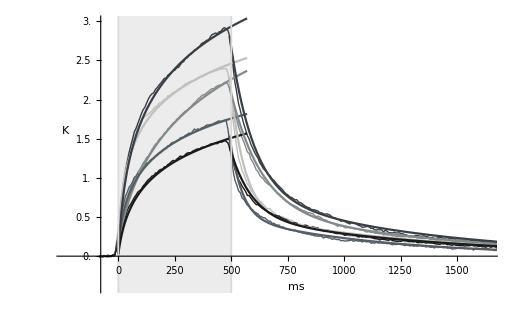

```mathematica
Show[grSDStdConVar,grRPlot,grFPlot]
```